```mathematica
redBluePlotConfig[n_]:=Table[RGBColor[(1-i),0,(i),(1-.7i)],{i,0,1,1/(n-1)}];
```

```mathematica
redBluePlotConfig[5]
```

{RGBColor[1, 0, 0, 1.],RGBColor[Rational[3, 4], 0, Rational[1, 4], 0.825],RGBColor[Rational[1, 2], 0, Rational[1, 2], 0.65],RGBColor[Rational[1, 4], 0, Rational[3, 4], 0.4750000000000001],RGBColor[0, 0, 1, 0.30000000000000004]}

## The snapshots needed for stress-fluctuation

```mathematica
Tlist1024={0.002,0.0025,0.0031,0.01, 0.01584893, 0.02511886 ,0.03981072, 0.06309573};
```

```mathematica
Tstring1024=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist1024
```

{0.00200000,0.00250000,0.00310000,0.01000000,0.01584893,0.02511886,0.03981072,0.06309573}

```mathematica
Tlist4096={0.002,0.0025,0.0031};
```

```mathematica
Tstring4096=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist4096
```

{0.00200000,0.00250000,0.00310000}

```mathematica
testdata=Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/nvt_N1024_p3.800_T",Tstring1024[[1]],"_0.nc"],"Data"];
```

```mathematica
timeNVT=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}];
```

```mathematica
stresses1024=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/stressNVT_N1024_p3.800_T",Tstring1024[[i]],"_0.csv"],"CSV"][[1]]*area,{i,Length[Tstring1024]}];
```

```mathematica
stresses1024=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/stressNVT_N1024_p3.800_T",Tstring1024[[4]],"_t10000000_",ToString[i],".csv"],"CSV"][[1]]*area,{i,9}];
```

```mathematica
insGs1024=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/insGNVT_N1024_p3.800_T",Tstring1024[[4]],"_t10000000_",ToString[i],".csv"],"CSV"][[1]],{i,9}];
```

```mathematica
insGs1024=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/insGNVT_N1024_p3.800_T",Tstring1024[[i]],"_0.csv"],"CSV"][[1]],{i,Length[Tstring1024]}];
```

```mathematica
stresses4096=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N4096/stressNVT_N4096_p3.800_T",Tstring1024[[i]],"_0.csv"],"CSV"][[1]]*4096,{i,Length[Tstring4096]}];
```

```mathematica
insGs4096=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N4096/insGNVT_N4096_p3.800_T",Tstring1024[[i]],"_0.csv"],"CSV"][[1]],{i,Length[Tstring4096]}];
```

```mathematica
sisf=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/nvt_SISF_N1024_p3.800_T",Tstring1024[[i]],"_0.csv"],"CSV"][[1]],{i,Length[Tstring1024]}];
```

```mathematica
Dimensions[stresses4096]
```

{3,100000}

```mathematica
data=Import["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/nvt_N1024_p3.800_T0.00200000_0.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[…],/postion→NumericArray[…],/time→NumericArray[…],/type→NumericArray[…],/velocity→NumericArray[…]|>

```mathematica
Length[insGs1024[[1]]]
```

100000

```mathematica
stresses1024[[3,1]]
```

0.00135804

```mathematica
inGsLong=Import["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/insGNVT_N1024_p3.800_T0.01000000_t1000000000_0.csv","CSV"][[1]];
```

```mathematica
stressesLong=Import["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/stressNVT_N1024_p3.800_T0.01000000_t1000000000_0.csv","CSV"][[1]]*1024;
```

### 10,000,000 snapshots

```mathematica
G2Long=Table[Mean[MovingMap[Variance,stressesLong,Quantity[ts[[t]],"Events"]]],{t,Length[ts]}];
```

## Moving mean and variance

```mathematica
Simplify[Mean[MovingMap[Mean,{a,b,c,d,e,f,g,h},Quantity[4,"Events"]]]]
```

1/20 (a+2 b+3 c+4 d+4 e+3 f+2 g+h)

```mathematica
ts=Table[Round[10^(1+0.2 t)],{t,0,30}]
```

{10,16,25,40,63,100,158,251,398,631,1000,1585,2512,3981,6310,10000,15849,25119,39811,63096,100000,158489,251189,398107,630957,1000000,1584893,2511886,3981072,6309573,10000000}

```mathematica
G1raw=Table[Table[Mean[MovingMap[Mean,insGs1024[[i]],Quantity[ts[[t]],"Events"]]],{t,Length[ts]}],{i,9}];
```

```mathematica
G2raw=Table[Table[Mean[MovingMap[Variance,stresses1024[[i]],Quantity[ts[[t]],"Events"]]],{t,Length[ts]}],{i,9}];
```

```mathematica
G1=1/area G1raw;
```

```mathematica
G2=Table[G2raw[[i]]/(area 0.01),{i,Length[G2raw]}];
```

```mathematica
G=G1-G2;
```

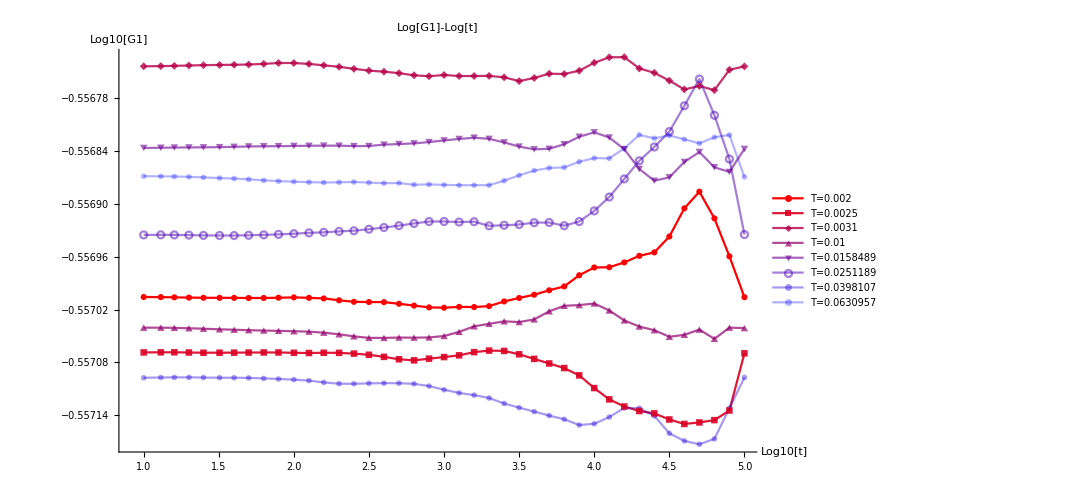

```mathematica
G1Plot=ListPlot[Table[Table[{Log10[ts[[t]]],Log10[G1[[i,t]]]},{t,Length[ts]}],{i,8}],PlotStyle->redBluePlotConfig[8],PlotLegends->Table[StringJoin["T=",ToString[Tlist1024[[i]]]],{i,8}],AxesLabel->{"Log10[t]","Log10[G1]"},ImageSize->800,PlotLabel->"Log[G1]-Log[t]",PlotMarkers->Automatic,Joined->True]
```

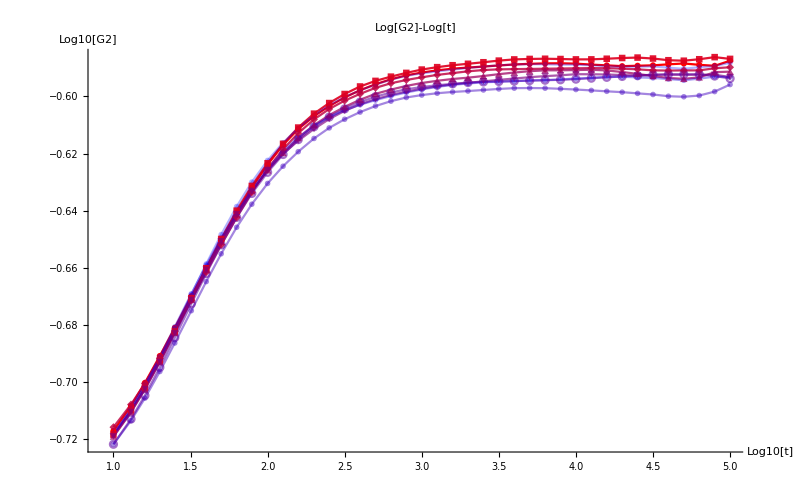

```mathematica
G2Plot=ListLinePlot[Table[Table[{Log10[ts[[t]]],Log10[G2[[i,t]]]},{t,Length[ts]}],{i,9}],PlotStyle->redBluePlotConfig[9],AxesLabel->{"Log10[t]","Log10[G2]"},ImageSize->800,PlotLabel->"Log[G2]-Log[t]",PlotMarkers->Automatic,Joined->True]
```

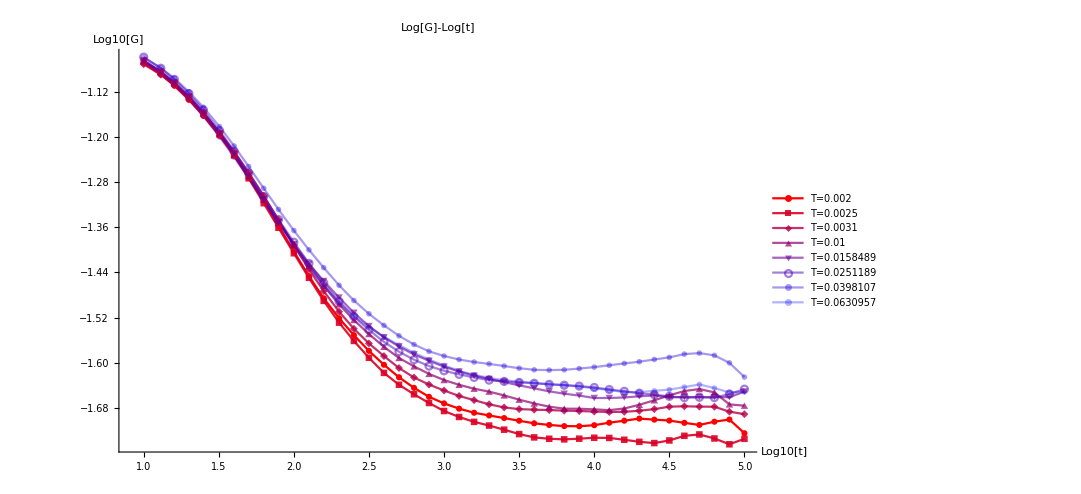

```mathematica
ListLinePlot[Table[Table[{Log10[ts[[t]]],Log10[G[[i,t]]]},{t,Length[ts]}],{i,1,8}],PlotStyle->redBluePlotConfig[8],PlotLegends->Table[StringJoin["T=",ToString[Tlist1024[[i]]]],{i,8}],AxesLabel->{"Log10[t]","Log10[G]"},ImageSize->800,PlotLabel->"Log[G]-Log[t]",PlotMarkers->Automatic,Joined->True]
```

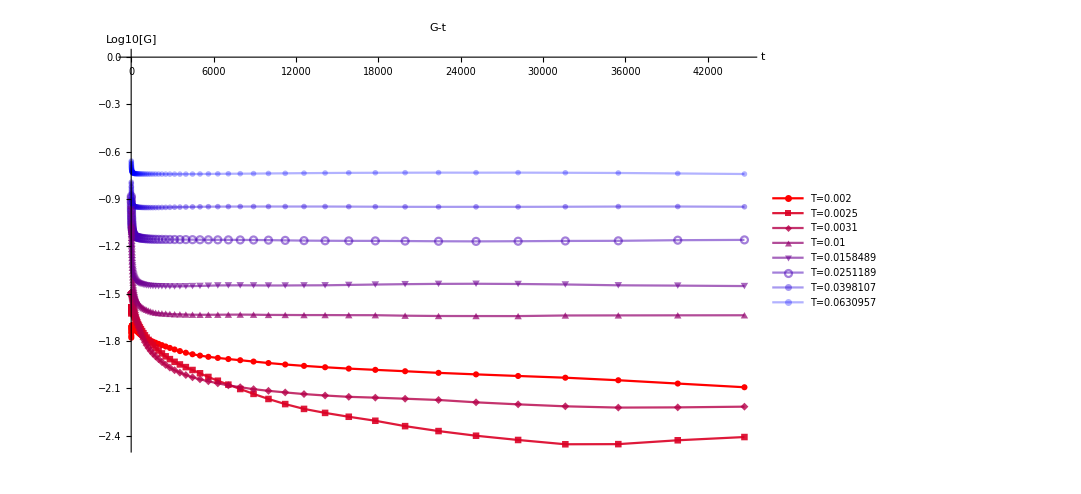

```mathematica
ListLinePlot[Table[Table[{ts[[t]],Log10[G1[[i,t]]-G2[[i,t]]]},{t,Length[ts]}],{i,1,8}],PlotStyle->redBluePlotConfig[8],PlotLegends->Table[StringJoin["T=",ToString[Tlist1024[[i]]]],{i,8}],AxesLabel->{"t","Log10[G]"},ImageSize->800,PlotLabel->"G-t",PlotMarkers->Automatic,Joined->True,PlotRange->All]
```

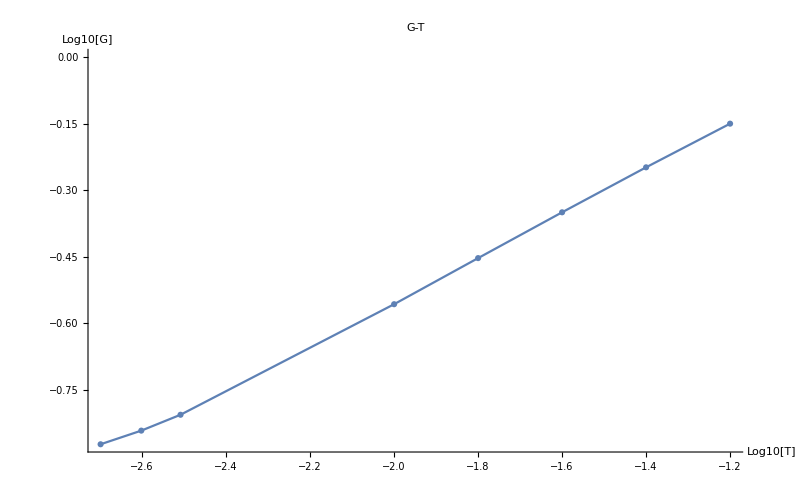

```mathematica
ListLinePlot[Table[{Log10[Tlist1024[[i]]],Log10[G1[[i,Length[G[[i]]]]]]},{i,8}],PlotMarkers->Automatic,AxesLabel->{"Log10[T]","Log10[G]"},ImageSize->800,PlotLabel->"G-T",PlotRange->All]
```

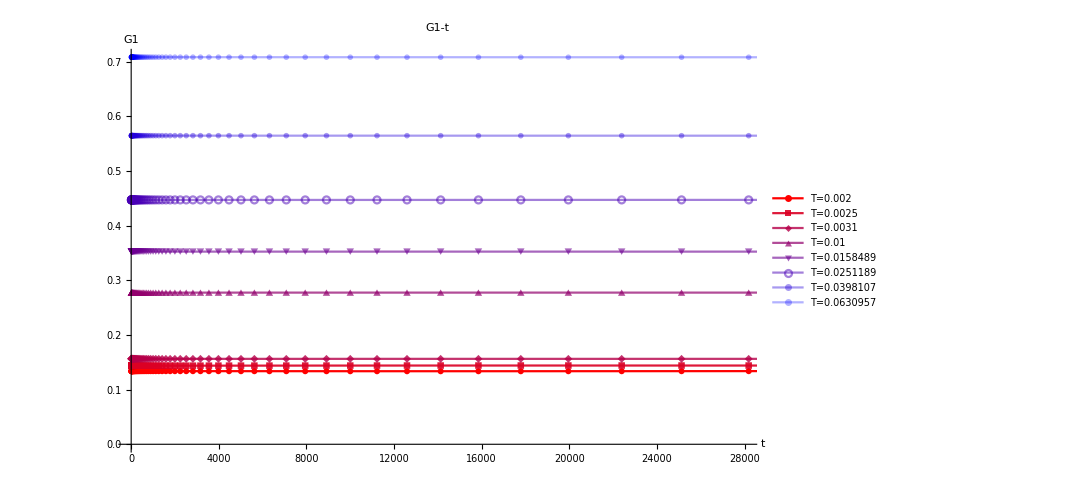

```mathematica
G1Plot=ListPlot[Table[Table[{ts[[t]],G1[[i,t]]},{t,Length[ts]}],{i,8}],PlotStyle->redBluePlotConfig[8],PlotLegends->Table[StringJoin["T=",ToString[Tlist1024[[i]]]],{i,8}],AxesLabel->{"t","G1"},ImageSize->800,PlotLabel->"G1-t",PlotMarkers->Automatic,Joined->True]
```

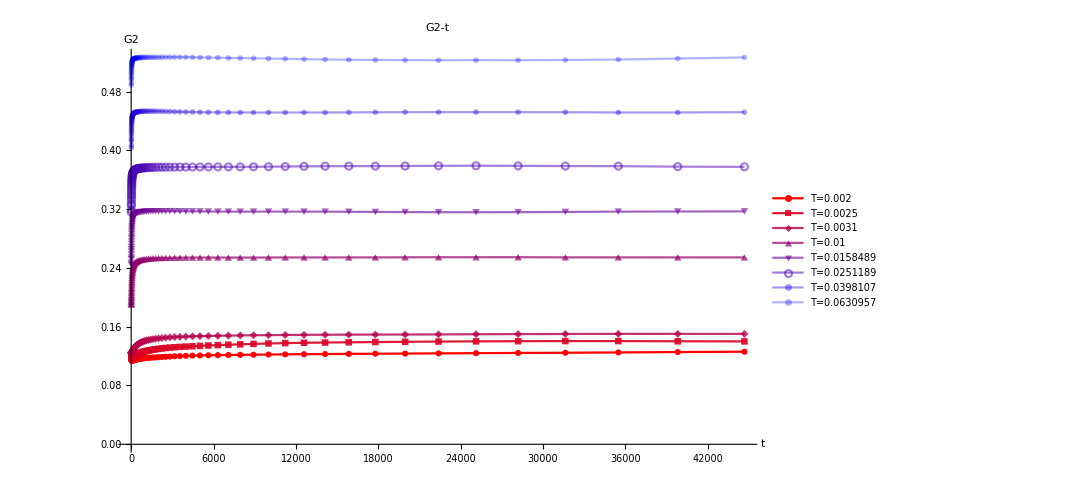

```mathematica
G2Plot=ListLinePlot[Table[Table[{ts[[t]],G2[[i,t]]},{t,Length[ts]}],{i,1,8}],PlotStyle->redBluePlotConfig[8],PlotLegends->Table[StringJoin["T=",ToString[Tlist1024[[i]]]],{i,8}],AxesLabel->{"t","G2"},ImageSize->800,PlotLabel->"G2-t",PlotMarkers->Automatic,Joined->True,PlotRange->All]
```

### High T

```mathematica
Tlist1024High={0.08 ,0.09, 0.10 ,0.11, 0.12, 0.13, 0.14};
```

```mathematica
Tstring1024High=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist1024High
```

{0.08000000,0.09000000,0.10000000,0.11000000,0.12000000,0.13000000,0.14000000}

```mathematica
Tlist1024High2={0.065,0.067,0.070};
```

```mathematica
Tstring1024High2=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist1024High2
```

{0.06500000,0.06700000,0.07000000}

```mathematica
tshigh=Table[Round[10^(1+0.05 t)],{t,0,80}]
```

{10,11,13,14,16,18,20,22,25,28,32,35,40,45,50,56,63,71,79,89,100,112,126,141,158,178,200,224,251,282,316,355,398,447,501,562,631,708,794,891,1000,1122,1259,1413,1585,1778,1995,2239,2512,2818,3162,3548,3981,4467,5012,5623,6310,7079,7943,8913,10000,11220,12589,14125,15849,17783,19953,22387,25119,28184,31623,35481,39811,44668,50119,56234,63096,70795,79433,89125,100000}

```mathematica
insG1024HighT2=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/insGNVT_N1024_p3.800_T",Tstring1024High2[[i]],"_t10000000_0.csv"],"CSV"][[1]],{i,Length[Tstring1024High2]}];
stresses1024HighT2=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/stressNVT_N1024_p3.800_T",Tstring1024High2[[i]],"_t10000000_0.csv"],"CSV"][[1]]*area,{i,Length[Tstring1024High2]}];
```

```mathematica
insG1024HighT=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/insGNVT_N1024_p3.800_T",Tstring1024High[[i]],"_t10000000_0.csv"],"CSV"][[1]],{i,Length[Tstring1024High]}];
stresses1024HighT=Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/stressNVT_N1024_p3.800_T",Tstring1024High[[i]],"_t10000000_0.csv"],"CSV"][[1]]*area,{i,Length[Tstring1024High]}];
```

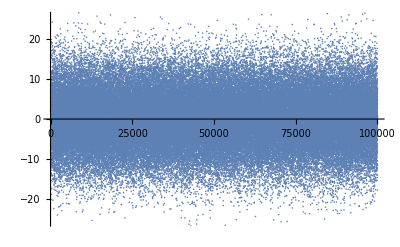

```mathematica
ListPlot[stresses1024HighT[[1]]]
```

```mathematica
G1rawHigh2=Table[Table[Mean[MovingMap[Mean,insG1024HighT2[[i]],Quantity[tshigh[[t]],"Events"]]],{t,Length[tshigh]}],{i,Length[Tlist1024High2]}];
```

```mathematica
G2rawHigh2=Table[Table[Mean[MovingMap[Variance,stresses1024HighT2[[i]],Quantity[tshigh[[t]],"Events"]]],{t,Length[tshigh]}],{i,Length[Tlist1024High2]}];
```

```mathematica
G1rawHigh=Table[Table[Mean[MovingMap[Mean,insG1024HighT[[i]],Quantity[tshigh[[t]],"Events"]]],{t,Length[tshigh]}],{i,Length[Tlist1024High]}];
```

```mathematica
G2rawHigh=Table[Table[Mean[MovingMap[Variance,stresses1024HighT[[i]],Quantity[tshigh[[t]],"Events"]]],{t,Length[tshigh]}],{i,Length[Tlist1024High]}];
```

```mathematica
G1High2=1/area G1rawHigh2;
```

```mathematica
G2High2=Table[G2rawHigh2[[i]]/(area Tlist1024High2[[i]]),{i,Length[Tlist1024High2]}];
```

```mathematica
GHigh2=G1High2-G2High2;
```

```mathematica
G1High=1/area G1rawHigh;
```

```mathematica
G2High=Table[G2rawHigh[[i]]/(area Tlist1024High[[i]]),{i,Length[Tlist1024High]}];
```

```mathematica
GHigh=G1High-G2High;
```

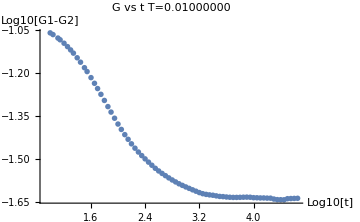
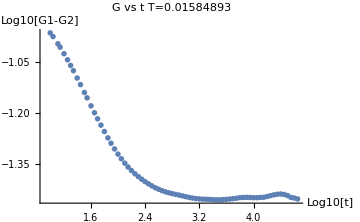
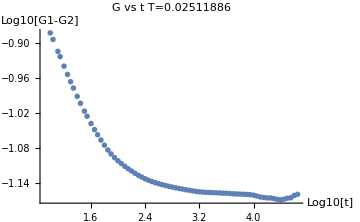
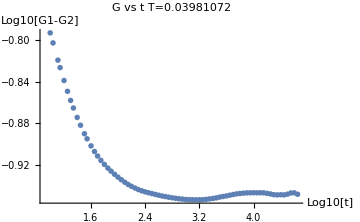
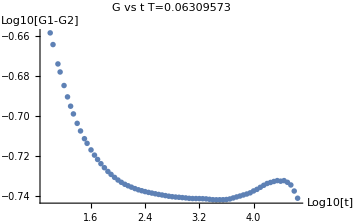

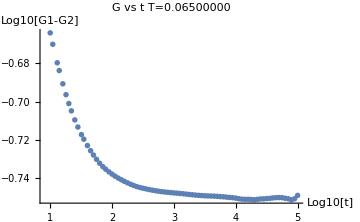
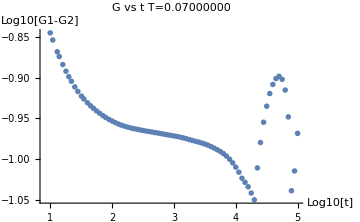
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Table[{Log10[tshigh[[t]]],Log10[G[[i,t]]]},{t,Length[ts]}],PlotRange->All,ImageSize->Medium,PlotLabel->"G vs t 
T="<>Tstring1024[[i]],AxesLabel->{"Log10[t]","Log10[G1-G2]"}],{i,4,8}]
Table[ListPlot[Table[{Log10[tshigh[[t]]],Log10[GHigh2[[i,t]]]},{t,Length[tshigh]}],PlotRange->All,ImageSize->Medium,PlotLabel->"G vs t
T="<>Tstring1024High2[[i]],AxesLabel->{"Log10[t]","Log10[G1-G2]"}],{i,3}]
```

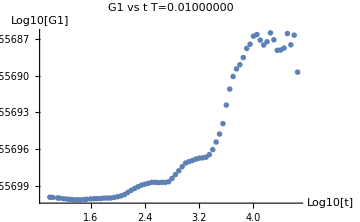
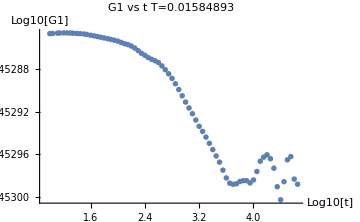
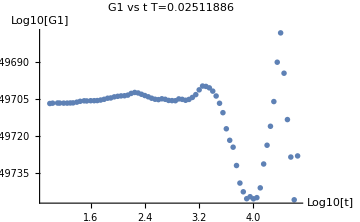
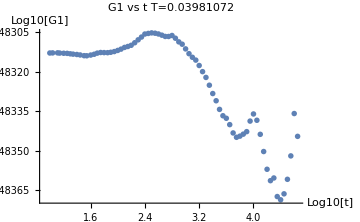
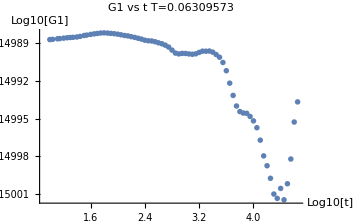

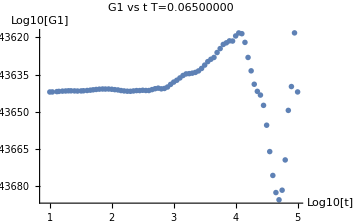
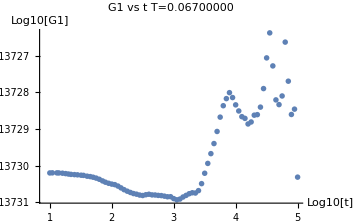
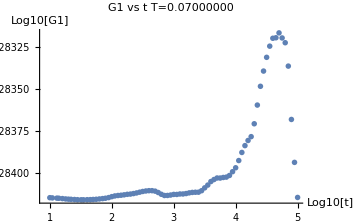

```mathematica
Table[ListPlot[Table[{Log10[tshigh[[t]]],Log10[G1[[i,t]]]},{t,Length[ts]}],PlotRange->All,ImageSize->Medium,PlotLabel->"G1 vs t
T="<>Tstring1024[[i]],AxesLabel->{"Log10[t]","Log10[G1]"}],{i,4,8}]
Table[ListPlot[Table[{Log10[tshigh[[t]]],Log10[G1High2[[i,t]]]},{t,Length[tshigh]}],PlotRange->All,ImageSize->Medium,PlotLabel->"G1 vs t
T="<>Tstring1024High2[[i]],AxesLabel->{"Log10[t]","Log10[G1]"}],{i,3}]
```

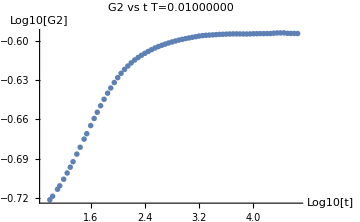
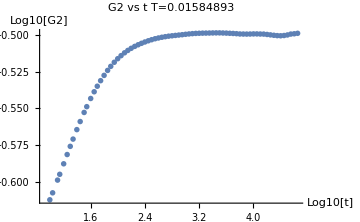
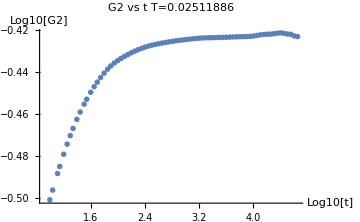
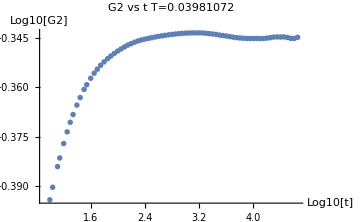
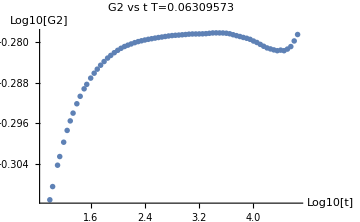

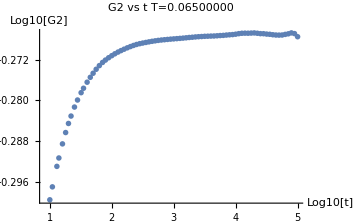
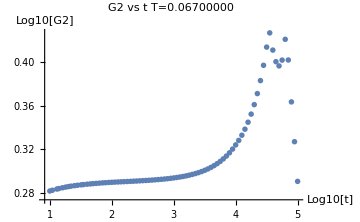
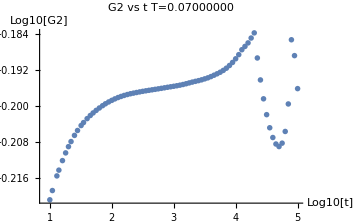

```mathematica
Table[ListPlot[Table[{Log10[tshigh[[t]]],Log10[G2[[i,t]]]},{t,Length[ts]}],PlotRange->All,ImageSize->Medium,PlotLabel->"G2 vs t
T="<>Tstring1024[[i]],AxesLabel->{"Log10[t]","Log10[G2]"}],{i,4,8}]
Table[ListPlot[Table[{Log10[tshigh[[t]]],Log10[G2High2[[i,t]]]},{t,Length[tshigh]}],PlotRange->All,ImageSize->Medium,PlotLabel->"G2 vs t
T="<>Tstring1024High2[[i]],AxesLabel->{"Log10[t]","Log10[G2]"}],{i,3}]
Table[ListPlot[Table[{Log10[tshigh[[t]]],Log10[G2High[[i,t]]]},{t,Length[tshigh]}],PlotRange->All,ImageSize->Medium,PlotLabel->"T="<>Tstring1024High[[i]]],{i,3}]
```

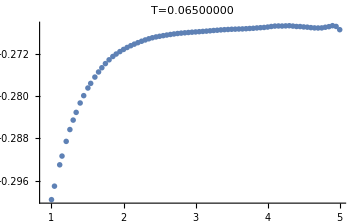
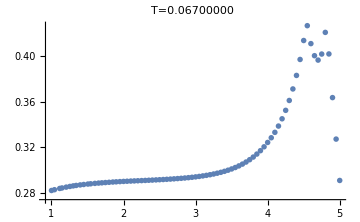
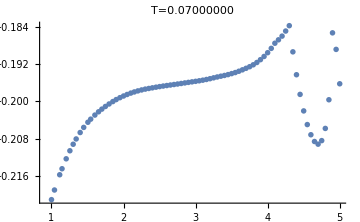

```mathematica
Table[ListPlot[Table[{Log10[tshigh[[t]]],Log10[G2High2[[i,t]]]},{t,Length[tshigh]}],PlotRange->All,ImageSize->Medium,PlotLabel->"T="<>Tstring1024High2[[i]]],{i,3}]
```

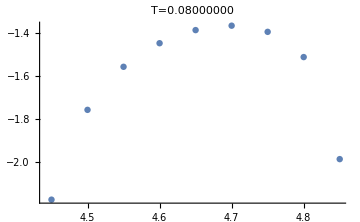
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Table[{Log10[tshigh[[t]]],Log10[GHigh[[i,t]]]},{t,Length[tshigh]}],PlotRange->All,ImageSize->Medium,PlotLabel->"T="<>Tstring1024High[[i]]],{i,3}]
```

```mathematica
Table[Log10[Variance[stresses1024HighT2[[i]]]/area Tlist1024High[[i]]],{i,Length[Tlist1024High2]}]
```

{-2.55149,-1.92895,-2.35112}

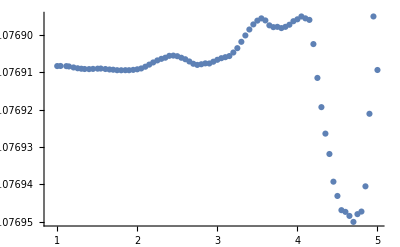

```mathematica
ListPlot[Table[{Log10[tshigh[[t]]],Log10[G1High[[2,t]]]},{t,Length[tshigh]}],PlotRange->All]
```

```mathematica
ListPlot[Table[{Log10[tshigh[[t]]],Log10[GHigh[[2,t]]]},{t,Length[tshigh]}]]
```

-Graphics-

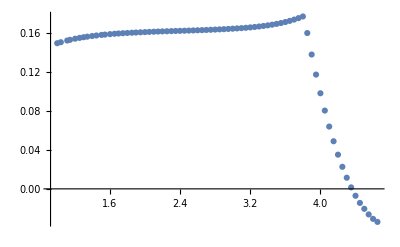

```mathematica
ListPlot[Table[{Log10[ts[[t]]],Log10[G2High2[[1,t]]]},{t,Length[ts]}]]
```

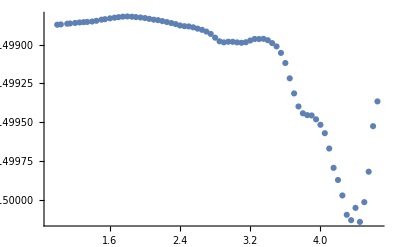

```mathematica
ListPlot[Table[{Log10[tshigh[[t]]],Log10[G1[[8,t]]]},{t,Length[ts]}]]
```

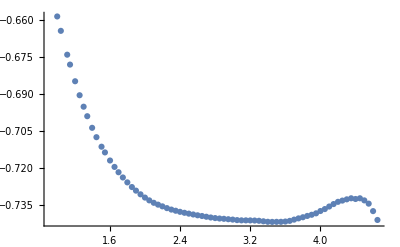

```mathematica
ListPlot[Table[{Log10[tshigh[[t]]],Log10[G[[8,t]]]},{t,Length[ts]}]]
```

```mathematica
GHigh[[1]]
```

{-0.354603,-0.357376,-0.361967,-0.363865,-0.366928,-0.369224,-0.371071,-0.372566,-0.374371,-0.375842,-0.377429,-0.378355,-0.379593,-0.380622,-0.381413,-0.38216,-0.382842,-0.3835,-0.384089,-0.384687,-0.385246,-0.385798,-0.386334,-0.386805,-0.387214,-0.387624,-0.38804,-0.388416,-0.388762,-0.389141,-0.389527,-0.389934,-0.390333,-0.390787,-0.391264,-0.391785,-0.392333,-0.392915,-0.393507,-0.394152,-0.394856,-0.395622,-0.396453,-0.397404,-0.398489,-0.399698,-0.401063,-0.402573,-0.404276,-0.406217,-0.408415,-0.410897,-0.413743,-0.417025,-0.420761,-0.424987,-0.429799,-0.382699,-0.324381,-0.272496,-0.226415,-0.18547,-0.149125,-0.116912,-0.0884845,-0.0635031,-0.0416495,-0.0227755,-0.00672158,0.00670396,0.0175563,0.0278541,0.0358663,0.0412786,0.0432847,0.0405163,0.030912,0.0103515,-0.0363778,-0.196078,-0.38885}

## Different sample size

```mathematica
G1Steps=Table[Table[1/area Mean[insGs1024[[i]][[1;;N]]],{N,samplesize}],{i,8,8}];
```

```mathematica
G2Steps=Table[Table[1/(area Tlist1024[[i]]) Variance[stresses1024[[i]][[1;;N]]],{N,samplesize}],{i,8,8}];
```

```mathematica
Gsteps=G1Steps-G2Steps;
```

```mathematica
G1StepsSpacing10=Table[Table[1/area Mean[insGs1024[[i]][[1;;N;;10]]],{N,samplesize}],{i,8}];
```

```mathematica
G2StepsSpacing10=Table[Table[1/(area Tlist1024[[i]]) Variance[stresses1024[[i]][[1;;N;;10]]],{N,samplesize}],{i,8}];
```

```mathematica
GstepsSpacing10=G1StepsSpacing10-G2StepsSpacing10;
```

```mathematica
G1StepsSpacing5=Table[Table[1/area Mean[insGs1024[[i]][[1;;N;;5]]],{N,samplesize}],{i,8}];
```

```mathematica
G2StepsSpacing5=Table[Table[1/(area Tlist1024[[i]]) Variance[stresses1024[[i]][[1;;N;;5]]],{N,samplesize}],{i,8}];
```

```mathematica
GstepsSpacing5=G1StepsSpacing5-G2StepsSpacing5;
```

```mathematica
G1StepsSpacing2=Table[Table[1/area Mean[insGs1024[[i]][[1;;N;;2]]],{N,samplesize}],{i,8}];
```

```mathematica
G2StepsSpacing2=Table[Table[1/(area Tlist1024[[i]]) Variance[stresses1024[[i]][[1;;N;;2]]],{N,samplesize}],{i,8}];
```

```mathematica
GstepsSpacing2=G1StepsSpacing2-G2StepsSpacing2;
```

```mathematica
G1Steps4096=Table[Table[1/4096 Mean[insGs4096[[i]][[1;;N]]],{N,samplesize}],{i,3}];
```

```mathematica
G2Steps4096=Table[Table[1/(4096 Tlist4096[[i]]) Variance[stresses4096[[i]][[1;;N]]],{N,samplesize}],{i,3}];
```

```mathematica
Gsteps4096=G1Steps4096-G2Steps4096;
```

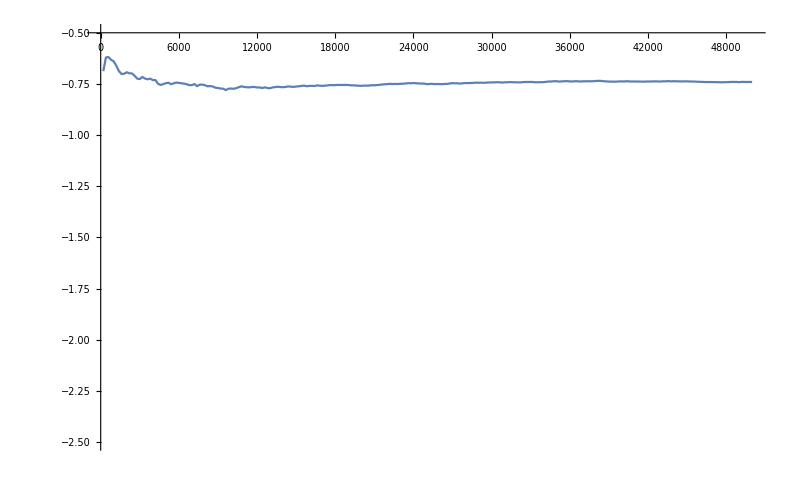

```mathematica
ListLinePlot[Table[{samplesize[[n]],Log10[Gsteps[[1,n]]]},{n,250}],PlotRange->{{0,50000},{-2.5,-0.5}}]
```

```mathematica
GNomalize=Table[Table[Gsteps[[i,N]]/Gsteps[[i,250]],{N,250}],{i,8}];
```

```mathematica
area=data[[1,1,4]]*data[[1,1,1]]
```

1024.

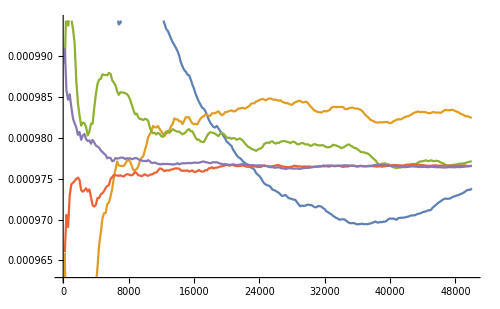

```mathematica
samplesize=Table[200 i,{i,250}];
ListLinePlot[Table[Table[{N,1/area Mean[insGs1024[[i]][[1;;N]]]/Mean[insGs1024[[i]]]},{N,samplesize}],{i,5}]]
```

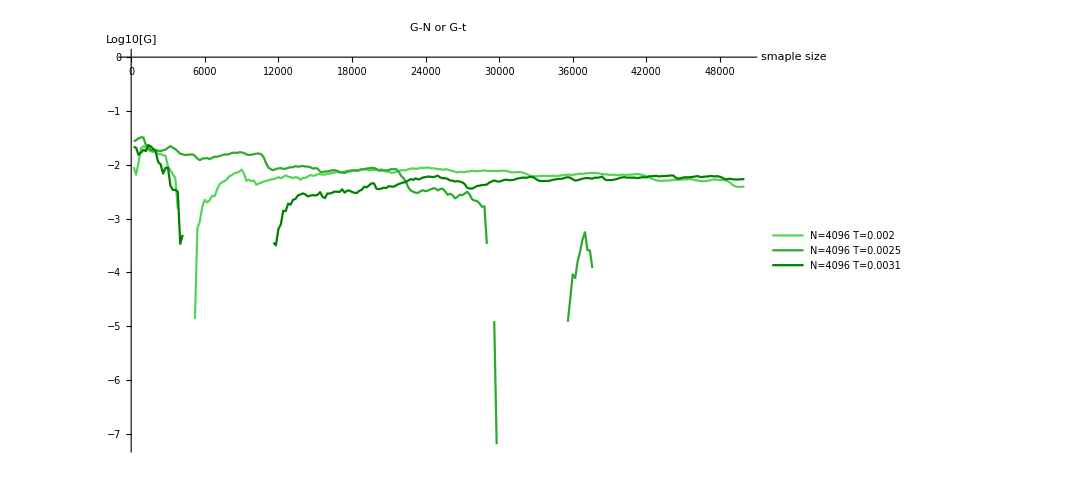

```mathematica
LowT4096=ListLinePlot[Table[Table[{samplesize[[n]],Log10[Gsteps4096[[i,n]]]},{n,250}],{i,3}],PlotStyle->Table[Blend[{GrayLevel[1-i/3],RGBColor[0,1,0]},0.5],{i,3}],PlotLegends->Table[StringJoin["N=4096 T=",ToString[Tlist4096[[i]]]],{i,3}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t",PlotRange->All]
```

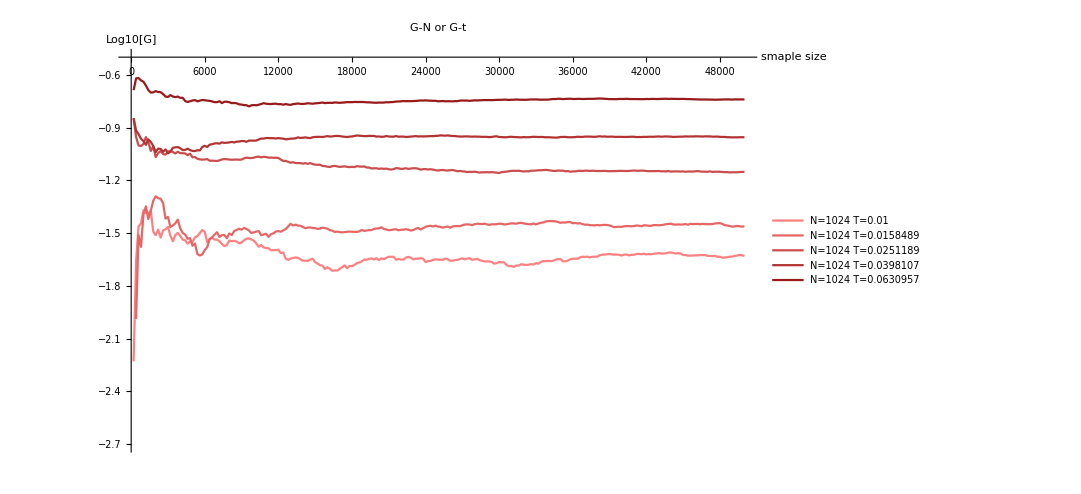

```mathematica
HighT=ListLinePlot[Table[Table[{samplesize[[n]],Log10[Gsteps[[i,n]]]},{n,250}],{i,4,8}],PlotStyle->Table[Blend[{GrayLevel[1-i/5],RGBColor[1,0,0]},0.5],{i,0,5}],PlotLegends->Table[StringJoin["N=1024 T=",ToString[Tlist1024[[i+3]]]],{i,5}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t",PlotRange->{Automatic,{-0.5,-2.7}}]
```

```mathematica
LowT=ListLinePlot[Table[Table[{samplesize[[n]],Log10[Gsteps[[i,n]]]},{n,250}],{i,1}],PlotStyle->Table[Blend[{GrayLevel[1-i/3],RGBColor[0,0,1]},0.5],{i,0,3}],PlotLegends->Table[StringJoin["N=1024 T=",ToString[Tlist1024[[i]]]],{i,8}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t"]
```

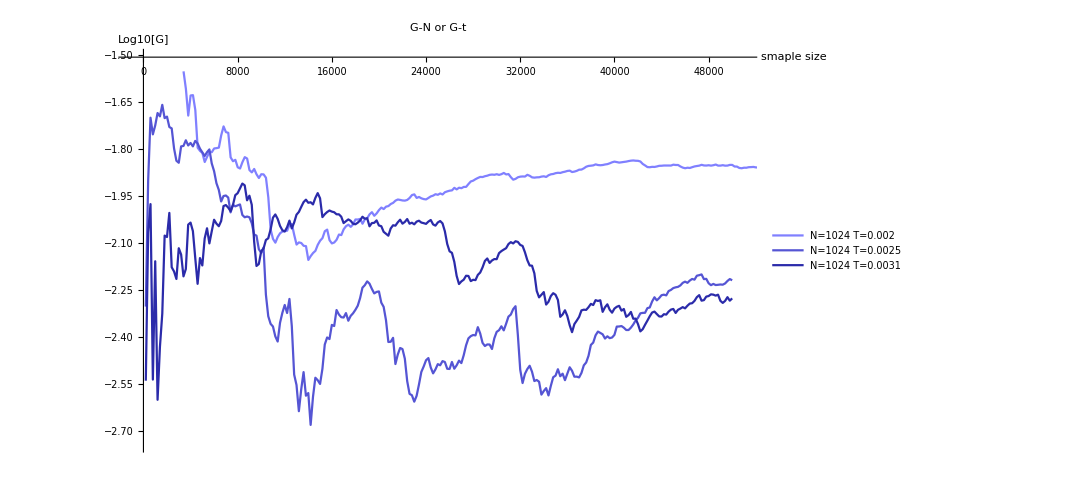

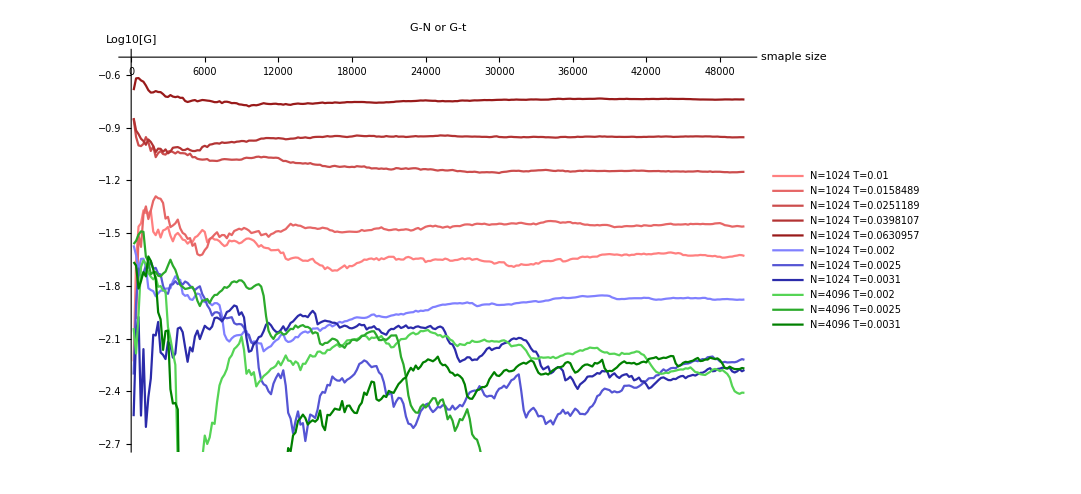

```mathematica
Show[HighT,LowT,LowT4096]
```

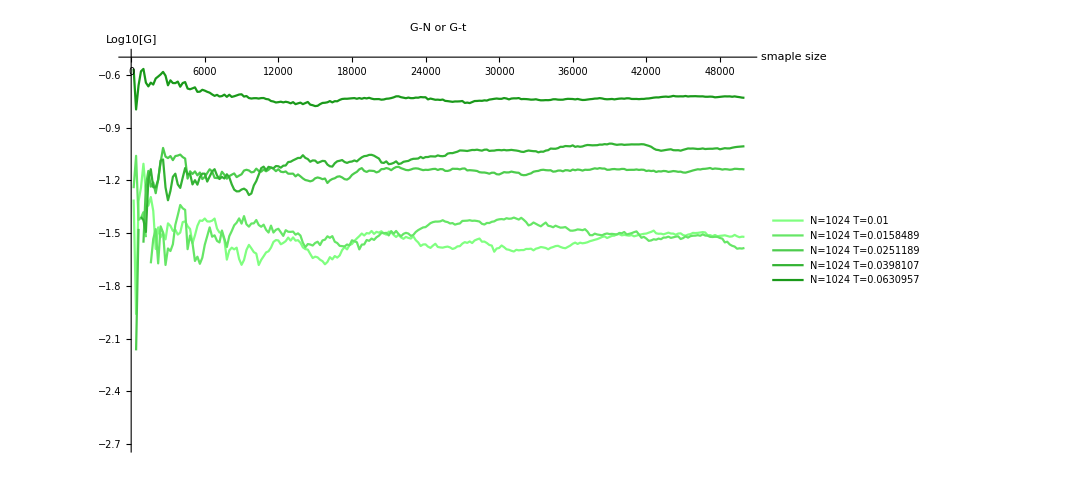

```mathematica
HighTSpacing10=ListLinePlot[Table[Table[{samplesize[[n]],Log10[GstepsSpacing10[[i,n]]]},{n,250}],{i,4,8}],PlotStyle->Table[Blend[{GrayLevel[1-i/5],RGBColor[0,1,0]},0.5],{i,0,5}],PlotLegends->Table[StringJoin["N=1024 T=",ToString[Tlist1024[[i+3]]]],{i,5}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t",PlotRange->{Automatic,{-0.5,-2.7}}]
```

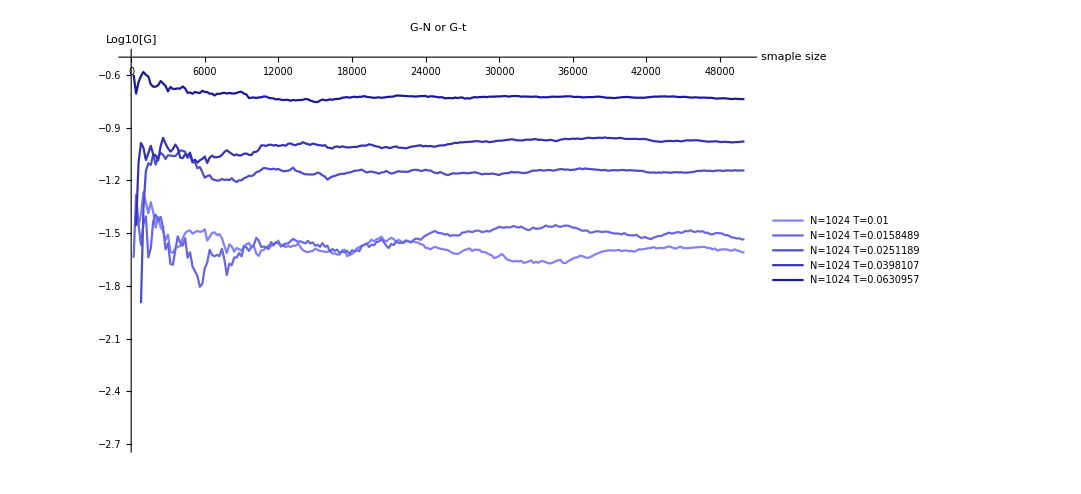

```mathematica
HighTSpacing5=ListLinePlot[Table[Table[{samplesize[[n]],Log10[GstepsSpacing5[[i,n]]]},{n,250}],{i,4,8}],PlotStyle->Table[Blend[{GrayLevel[1-i/5],RGBColor[0,0,1]},0.5],{i,0,5}],PlotLegends->Table[StringJoin["N=1024 T=",ToString[Tlist1024[[i+3]]]],{i,5}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t",PlotRange->{Automatic,{-0.5,-2.7}}]
```

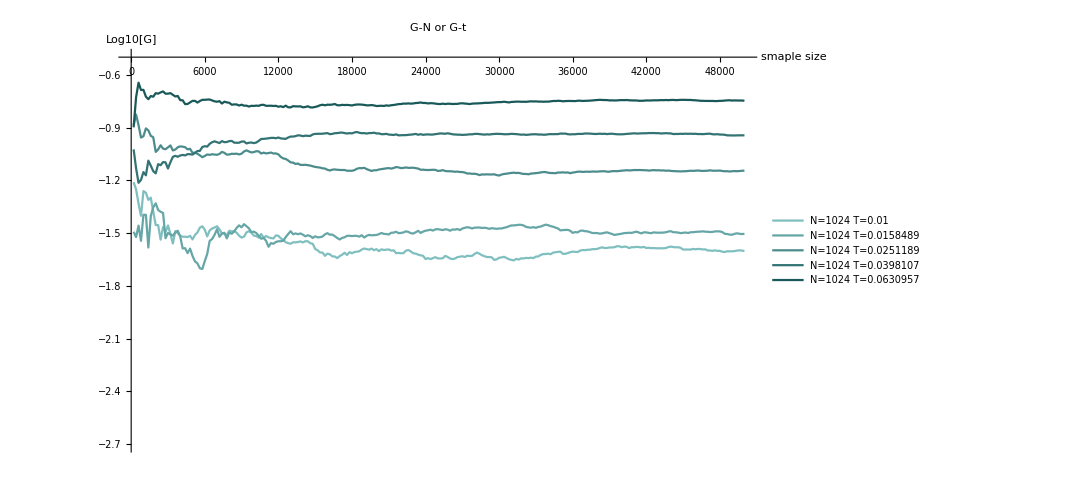

```mathematica
HighTSpacing2=ListLinePlot[Table[Table[{samplesize[[n]],Log10[GstepsSpacing2[[i,n]]]},{n,250}],{i,4,8}],PlotStyle->Table[Blend[{GrayLevel[1-i/5],RGBColor[0,0.5,0.5]},0.5],{i,0,5}],PlotLegends->Table[StringJoin["N=1024 T=",ToString[Tlist1024[[i+3]]]],{i,5}],AxesLabel->{"smaple size","Log10[G]"},ImageSize->800,PlotLabel->"G-N or G-t",PlotRange->{Automatic,{-0.5,-2.7}}]
```

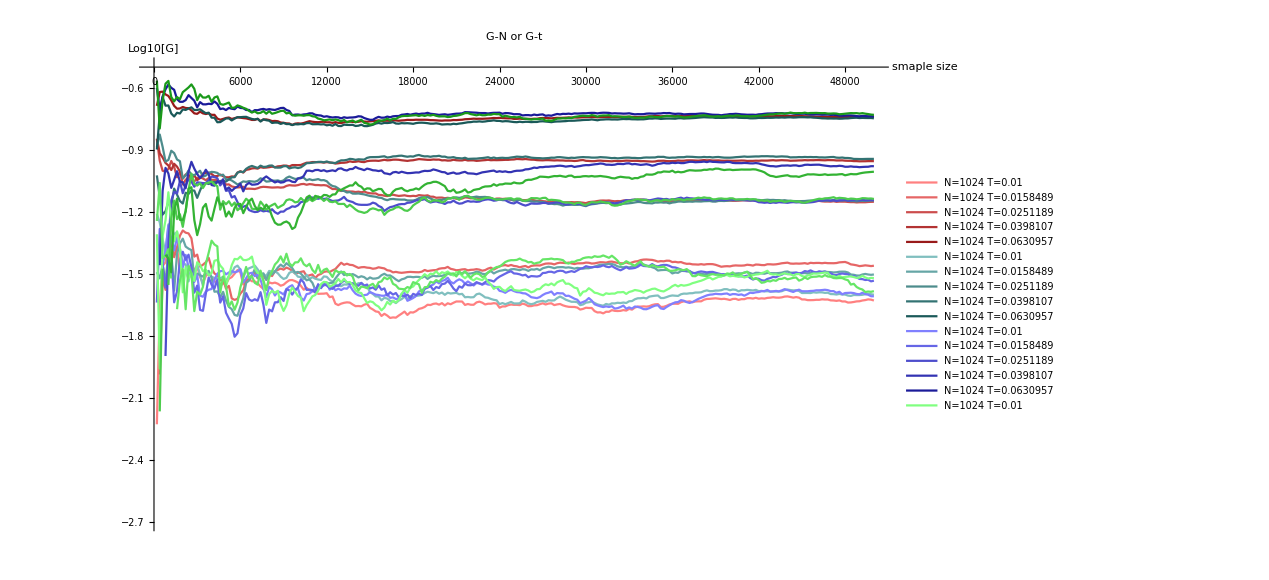

```mathematica
Show[HighT,HighTSpacing2,HighTSpacing5,HighTSpacing10]
```

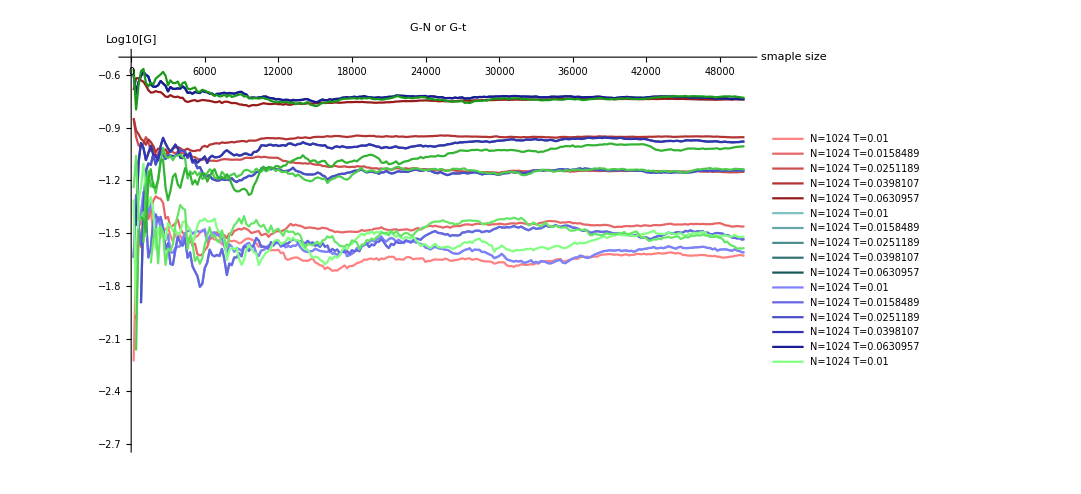

```mathematica
Show[HighT,HighTSpacing2,HighTSpacing5,HighTSpacing10]
```

```mathematica
Gsteps[[1;;2]][[1]]
```

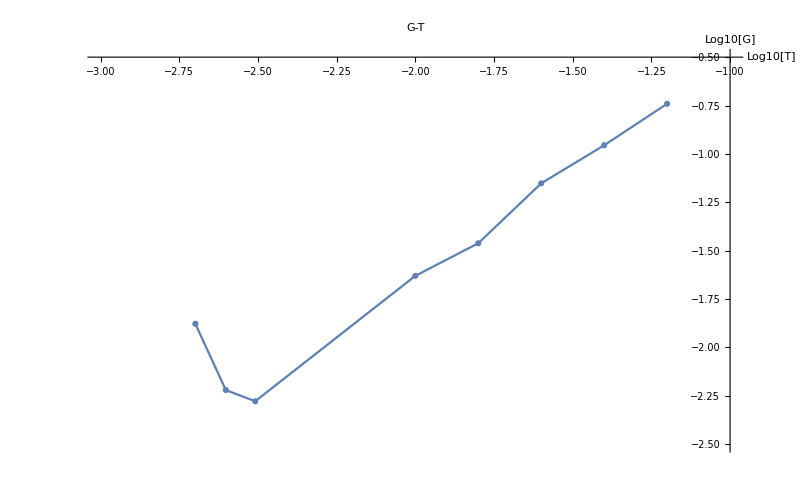

```mathematica
ListLinePlot[Table[{Log10[Tlist1024[[i]]],Log10[Gsteps[[i,250]]]},{i,8}],PlotMarkers->Automatic,AxesLabel->{"Log10[T]","Log10[G]"},ImageSize->800,PlotLabel->"G-T",PlotRange->{{-3,-1},{-2.5,-0.5}}]
```

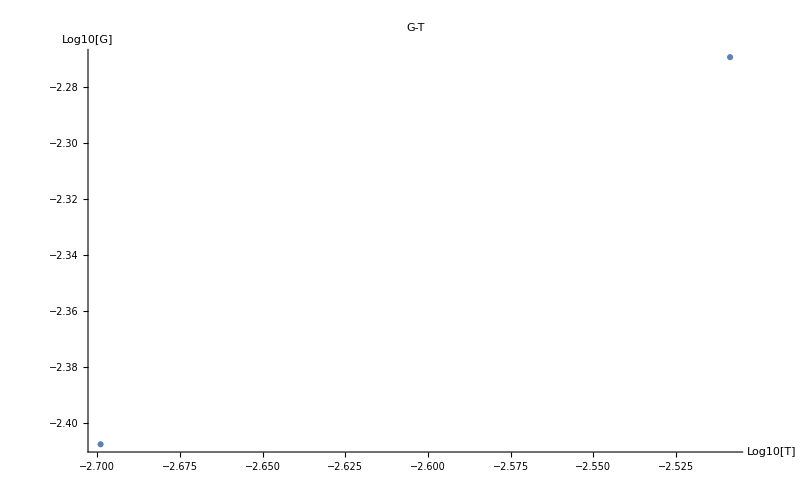

```mathematica
ListLinePlot[Table[{Log10[Tlist4096[[i]]],Log10[Gsteps4096[[i,250]]]},{i,3}],PlotMarkers->Automatic,AxesLabel->{"Log10[T]","Log10[G]"},ImageSize->800,PlotLabel->"G-T"]
```

```mathematica
Table[{Log10[Tlist1024[i]],Log10[Gsteps[[i,250]]]},{i,2}]
```

{{Log[{0.002,0.0025,0.0031,0.01,0.0158489,0.0251189,0.0398107,0.0630957}[1]]/Log[10],-1.87739},{Log[{0.002,0.0025,0.0031,0.01,0.0158489,0.0251189,0.0398107,0.0630957}[2]]/Log[10],-2.22004}}

```mathematica
Length[sisf[[1]]]
```

35

```mathematica
timeNVT[[35]]
```

63095.7

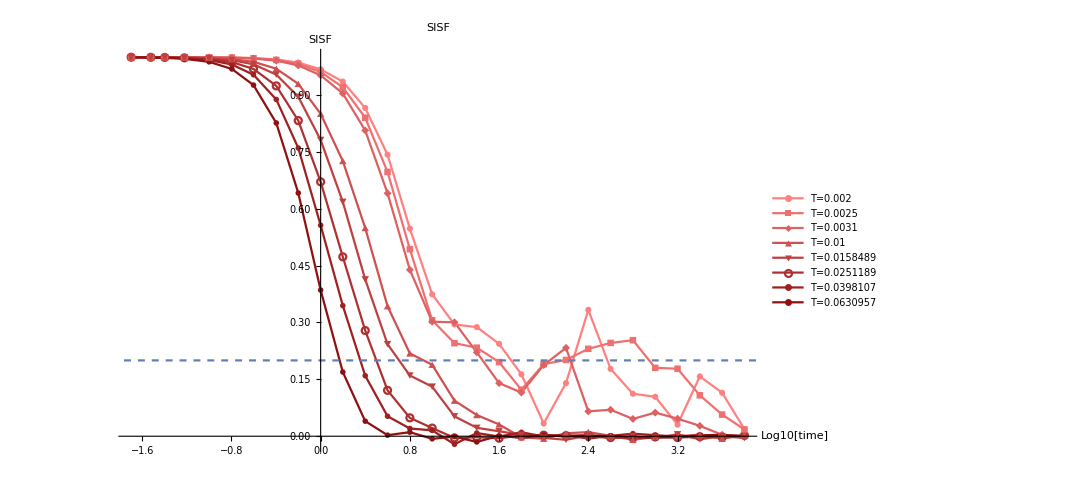

```mathematica
SISFPLOT=ListLinePlot[Table[Table[{Log10[timeNVT[[time]]],sisf[[i,time]]},{time,30}],{i,8}],PlotLegends->Table[StringJoin["T=",ToString[Tlist1024[[i]]]],{i,8}],AxesLabel->{"Log10[time]","SISF"},PlotStyle->Table[Blend[{GrayLevel[1-i/8],RGBColor[1,0,0]},0.5],{i,0,8}],PlotMarkers->Automatic,ImageSize->800,PlotLabel->"SISF"];
tau=Plot[0.2,{x,-10,100},PlotStyle->Dashed];
Show[SISFPLOT,tau]
```

```mathematica
10^0.2
```

1.58489

$Aborted

```mathematica
test=Import["/home/chengling/Research/Project/Cell/AnalyticalG/data/N1024/nvt_N1024_p3.800_T0.01000000_t0_1000000000.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[…],/postion→NumericArray[…],/time→NumericArray[…],/type→NumericArray[…],/velocity→NumericArray[…]|>

```mathematica
test[[4]][[43,1]]
```

2.52189×10^6